# Solving Equations

Lesson: Solving Equationshttps://vimeo.com/ondemand/mathematica/803811057Nonehttps://vimeo.com/ondemand/mathematica/803811057HyperlinkActionRecycledHyperlinkActive
Course: Mathematica Essentials

## One Equation / One Unknown

```mathematica
Solve[2x^2+3==7,x]
```

{{x→-√2},{x→√2}}

```mathematica
Solve[2 x+b==c,x]
```

{{x→1/2 (-b+c)}}

## Solutions as Rules

```mathematica
xsol=Solve[3x+1==0,x]
```

{{x→-1/3}}

```mathematica
x^2+x+1/.xsol
```

{7/9}

```mathematica
ysol=Solve[2y^2-y-1==0,y]
```

{{y→-1/2},{y→1}}

```mathematica
3/y/.ysol
```

{-6,3}

```mathematica
(* Solutions to second equation *)
y/.ysol
```

{-1/2,1}

## Number of Solutions

```mathematica
Solve[x+1==x+2,x]
```

{}

```mathematica
Solve[2x^3-x+1==0,x]
```

{{x→-1},{x→1/2-ⅈ/2},{x→1/2+ⅈ/2}}

```mathematica
Solve[Sin[x]+Cos[x]==0,x]
```

{{x→ConditionalExpression[-π/4+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[(3 π)/4+2 π C[1], C[1]∈ℤ]}}

```mathematica
Solve[x+1==1+x,x]
```

{{}}

## Infinitely Many Solutions

```mathematica
Solve[Sin[x]+Cos[x]==0,x]
```

{{x→ConditionalExpression[-π/4+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[(3 π)/4+2 π C[1], C[1]∈ℤ]}}

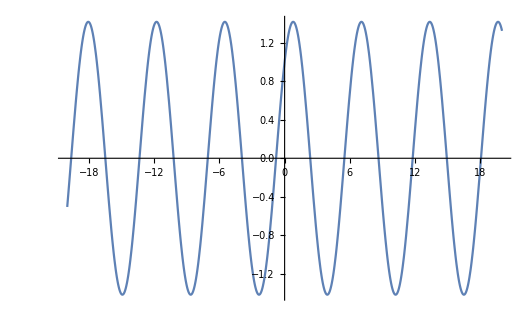

```mathematica
Plot[Sin[x]+Cos[x],{x,-20,20}]
```

```mathematica
sols=Table[{x->-π/4+2 π (n)},{n,-10,10}]
```

{{x→-(81 π)/4},{x→-(73 π)/4},{x→-(65 π)/4},{x→-(57 π)/4},{x→-(49 π)/4},{x→-(41 π)/4},{x→-(33 π)/4},{x→-(25 π)/4},{x→-(17 π)/4},{x→-(9 π)/4},{x→-π/4},{x→(7 π)/4},{x→(15 π)/4},{x→(23 π)/4},{x→(31 π)/4},{x→(39 π)/4},{x→(47 π)/4},{x→(55 π)/4},{x→(63 π)/4},{x→(71 π)/4},{x→(79 π)/4}}

```mathematica
Sin[x]+Cos[x]/.sols
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
notsols=Table[{x->-π/4+2 π (n)},{n,0.3,3.4,0.25}]
```

{{x→1.09956},{x→2.67035},{x→4.24115},{x→5.81195},{x→7.38274},{x→8.95354},{x→10.5243},{x→12.0951},{x→13.6659},{x→15.2367},{x→16.8075},{x→18.3783},{x→19.9491}}

```mathematica
Sin[x]+Cos[x]/.notsols
```

{1.345,-0.437016,-1.345,0.437016,1.345,-0.437016,-1.345,0.437016,1.345,-0.437016,-1.345,0.437016,1.345}

## Forms of Solutions

```mathematica
Solve[-3x+5==7,x]
```

{{x→-2/3}}

```mathematica
Solve[3x^2+2x+5==0,x]
```

{{x→1/3 (-1-ⅈ √14)},{x→1/3 (-1+ⅈ √14)}}

```mathematica
Solve[x^3+2 x+1==0,x]
```

{{x→Root-0.453Root[1+2 #1+#1^3&,1]-0.4533976515164039},{x→Root0.227-1.47 ⅈRoot[1+2 #1+#1^3&,2]0.22669882575820188},{x→Root0.227+1.47 ⅈRoot[1+2 #1+#1^3&,3]0.22669882575820188}}

```mathematica
N[Root"-0.453"Root[1+2 #1+#1^3&,1]-0.45339765151640377,100]
```

-0.4533976515164037676447465390001921888668844249650776598816632854323332304211686056678725148496405998

## System of Equations

```mathematica
sols=Solve[{y==x^2,y==2x+5},{x,y}]
```

{{x→1-√6,y→7-2 √6},{x→1+√6,y→7+2 √6}}

```mathematica
y==x^2/.sols
```

{True,True}

```mathematica
y==2x+5/.sols
```

{True,True}

```mathematica
N[sols]
```

{{x→-1.44949,y→2.10102},{x→3.44949,y→11.899}}

```mathematica
Solve[{2x+3y-z==1,x+2y+3z==0,7x-y+11z==13},{x,y,z}]
```

{{x→168/95,y→-81/95,z→-2/95}}

```mathematica
Solve[{x+y+z==1,2x-3y+5z==7},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→-1/4-(3 x)/8,z→5/4-(5 x)/8}}

## Numerical Approximations

```mathematica
NSolve[2 x^2+5x-1/3==0,x]
```

{{x→-2.56498},{x→0.0649778}}

```mathematica
NSolve[{x^2-y^2==1,x^2/9+y^2/16==1},{x,y}]
```

{{x→2.47386,y→2.26274},{x→-2.47386,y→-2.26274},{x→-2.47386,y→2.26274},{x→2.47386,y→-2.26274}}

```mathematica
NSolve[{x^2-y^2==1,x^2/9+y^2/16==1},{x,y},WorkingPrecision->10]
```

{{x→-2.47386338,y→-2.2627417},{x→2.47386338,y→2.2627417},{x→2.47386338,y→-2.2627417},{x→-2.47386338,y→2.2627417}}

```mathematica
TableForm[%]
```

x→-2.47386338 | y→-2.2627417
x→2.47386338 | y→2.2627417
x→2.47386338 | y→-2.2627417
x→-2.47386338 | y→2.2627417

## Beyond “Solve”

```mathematica
Solve[x^2+5Sin[x]-3==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-3+x^2+5 Sin[x]==0,x]

```mathematica
?FindRoot
```

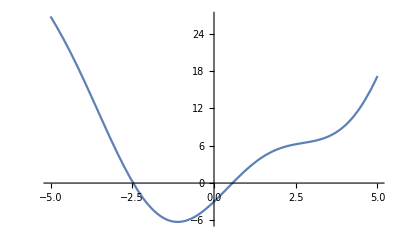

```mathematica
Plot[x^2+5Sin[x]-3,{x,-5,5}]
```

```mathematica
FindRoot[x^2+5Sin[x]-3,{x,-2}]
```

{x→-2.47116}

```mathematica
FindRoot[x^2+5Sin[x]-3,{x,1}]
```

{x→0.56569}

```mathematica
FindRoot[x^2+5Sin[x]-3,{x,1},WorkingPrecision->25]
```

{x→0.5656904765426557699477696}